## Molecular Forces

If, in some cataclysm, all of scientific knowledge were to be destroyed, and only one sentence passed on to the next generations of creatures, what statement would contain the most information in the fewest words? I believe it is the atomic hypothesis (or the atomic fact, or whatever you wish to call it) that all things are made of atoms—little particles that move around in perpetual motion, attracting each other when they are a little distance apart, but repelling upon being squeezed into one another. In that one sentence, you will see, there is an enormous amount of information about the world, if just a little imagination and thinking are applied.

Richard Feynman, The Feynman Lectures on Physics, Chapter 1, Volume I (Feynman, Leighton, and Sands) URL

## The Lennard Jones Potential

The Lennard-Jones Potential

The Lennard-Jones potential is a model for a particle's potential energy when it is separated from another particle.  The model is simple—particles attract each other when they are far apart and repulse when they are very near.  Nevertheless, the information that we will compute and visualize is considerable—especially when there are many interacting particles.

All of the physics and its consequences derive from the shape of the potential:

-Graphics-

When the distance is small, the potential decreases with increasing distance. The force is positive and repulsive because force is minus the gradient of potential energy.

When the distance is large, the slope is positive and so the force is negative: the particles attract.   We could construct many functions that behave like this; the Lennard-Jones potential is a simple choice. 
.00Th .00  .00y.00y.00.00y.00.00yy.00Th. .. ere

### Non-Dimensional Form of the Lennard-Jones Potential

We’ll drone about non-dimensionalizing (see Chapter X). For now, just trust us, it makes life easier and the physics more intuitive than putting in units.  There can never be physics in units—units are invented by humans.

We will do the non-dimensionalization as part of this example.  The Lennard-Jones potential is often written as

The a and b are the magnitudes of the attractive and repulsive potentials; they would be different for other particles.  They have strange units:  and .  

However, we claim that only the function’s form matters.  We can re-express the Lennard-Jones potential in terms of the form’s shape.  Because we have the two parameters a and b, we free to express these in terms of any other two parameters. Let’s define r_min as the position where minimum occurs and -E_min as the value of that minimum (Wikipedia has a different choice), we will need to solve two equations in two unknowns:

```mathematica
uLJP = a/r^12 - b/r^6;
```

```mathematica
minimumCondition = (0 == D[uLJP,r]/.r->rMin)
valueAtMinimumEquation = (-eMin == uLJP/.r-> rMin)
```

0==-(12 a)/rMin^13+(6 b)/rMin^7

-eMin==a/rMin^12-b/rMin^6

Solving for a and b in terms of rMin and eMin

```mathematica
abSolutions = Solve[{minimumCondition,valueAtMinimumEquation},{a,b}]
```

{{a→eMin rMin^12,b→2 eMin rMin^6}}

We re-express the potential by replacing the a and b.

```mathematica
uEminRmin = uLJP/.abSolutions[[1]]
```

-(2 eMin rMin^6)/r^6+(eMin rMin^12)/r^12

Notice how the units work out right. The potential has the same units as eMin [energy] and the units of each distance term are cancelled by an equivalent power of rMin.

We can write a non-dimensional form of the potential by: (i) introducing a non-dimensional length ρ=r/rMin; and (ii) divide the potential by the energy quantity.

```mathematica
uLJPρ = uEminRmin/.r-> ρ rMin
```

eMin/ρ^12-(2 eMin)/ρ^6

We like to use Greek characters to indicate non-dimensional quantities:

```mathematica
υLJP =Simplify[ uLJPρ/eMin]
```

1/ρ^12-2/ρ^6

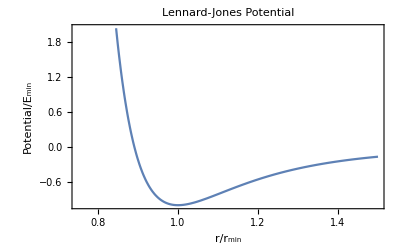

```mathematica
Plot[υLJP,{ρ,3/4,3/2},
 PlotLabel-> "Lennard-Jones Potential",
FrameLabel->{"r/r_min","Potential/E_min"},
Frame->True
]
```

Notice how we use the non-dimensionalization definitions in the plot labels instead of the symbols.  This makes plots easier to understand and less ambiguous.

### Solving F=m a for two particles interacting via the Lennard-Jones potential

We can write down Newton’s equation for our system.  The particle separation now has to be a function of time:

```mathematica
uEminRmin=uEminRmin/.r->r[t]
```

(eMin rMin^12)/r[t]^12-(2 eMin rMin^6)/r[t]^6

Force is minus the derivative of potential (it is also function of time)

```mathematica
force =- D[uEminRmin,r[t]]
```

(12 eMin rMin^12)/r[t]^13-(12 eMin rMin^6)/r[t]^7

```mathematica
massTimesAcceleration =mass  D[r[t],{t,2}]
```

mass r''[t]

Comment : 
When to non - dimensionalize and when not to.We had a nice non-dimensional form before in 1/ρ^12-2/ρ^6 why did we stop using it?

When new quantities—or new physics—are introduced (here time and mass), there are going to be new things to non-dimensionalize.  To do these subsequent non-dimensionalizations we will want to keep track of the units.  So, we go back to the last form that had the relevant units. You will see why.

Solving the second-order differential equation (Newton’s equation)

```mathematica
newtonsEquation = (0 == force - massTimesAcceleration)
```

0==(12 eMin rMin^12)/r[t]^13-(12 eMin rMin^6)/r[t]^7-mass r''[t]

Using DSolve and crossing our fingers:
(the following might take a while, but it should come back with a solution)

```mathematica
DSolve[newtonsEquation,r,t]
```

Solve[(AppellF1[7/6,1/2,1/2,13/6,-((mass C[1] r[t]^6)/(2 eMin rMin^6+√2 √(eMin rMin^12 (2 eMin+mass C[1])))),(mass C[1] r[t]^6)/(-2 eMin rMin^6+√2 √(eMin rMin^12 (2 eMin+mass C[1])))]^2 r[t]^2 (2 eMin rMin^6-√2 √(eMin rMin^12 (2 eMin+mass C[1]))+mass C[1] r[t]^6) (2 eMin rMin^6+√2 √(eMin rMin^12 (2 eMin+mass C[1]))+mass C[1] r[t]^6))/(49 (2 eMin rMin^6-√2 √(eMin rMin^12 (2 eMin+mass C[1]))) (2 eMin rMin^6+√2 √(eMin rMin^12 (2 eMin+mass C[1]))) (C[1]-(2 eMin rMin^6 (rMin^6-2 r[t]^6))/(mass r[t]^12)))==(t+C[2])^2,r[t]]

It did give a solution, but it isn’t very obvious how we might use it, and some of the terms in the solution may be unfamiliar like AppellF1[7/6,1/2,1/2,13/6,…].  We might think that adding initial conditions might help, but it doesn’t.

```mathematica
DSolve[{newtonsEquation, r[0]==1,r'[0]==0},r,t]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

So, we can’t find useful closed form solution. What do we do?

### The Harmonic Oscillator Approximation.

We can find the second order approximation to the Lennard-Jones Potential around the equilibrium point r=r_min.

```mathematica
υLJP
```

1/ρ^12-2/ρ^6

```mathematica
parabolicApproximation = Series[υLJP,{ρ,1,2}]
```

-1+36 (ρ-1)^2+O[ρ-1]^3

There is a term “+ O[ρ-1]^3” at the end of the Series expansion—it means “ plus terms on the order of (ρ-1)^3 and higher”.  This is a reminder that the expression is an approximation.  We are expanding around ρ=1, so we expect that those extra terms should be small.

We can get rid of the “O” by using Normal. 

Near the minimum, we have an equation for a parabola that we can compare the Lennard-Jones potential

```mathematica
parabolicApproximation = Normal[Series[υLJP,{ρ,1,2}]]
```

-1+36 (-1+ρ)^2

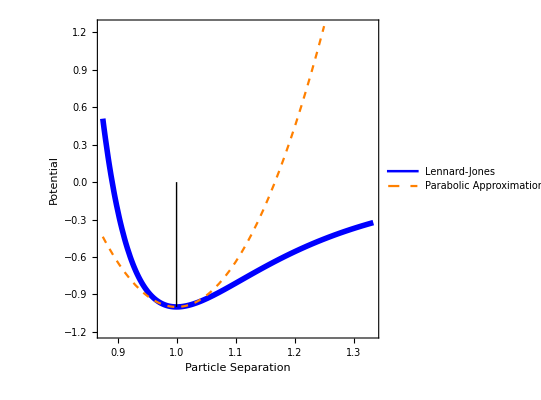

```mathematica
Plot[
{υLJP,parabolicApproximation},{ρ,7/8,4/3},

]
```

```mathematica
approximateLJPotential = 
Normal[Series[uEminRmin,{r[t],rMin,2}]]
```

-eMin+(36 eMin (-rMin+r[t])^2)/rMin^2

It is handy to replace the separation with the distance from the minimum: Δr[t] = r[t] - r_min

```mathematica
approximateLJPotential=approximateLJPotential/.r[t]-> deltaR[t] + rMin
```

-eMin+(36 eMin deltaR[t]^2)/rMin^2

We will write the  harmonic approximation for the Newton’s equation as 0 = rhs

```mathematica
harmonicForce = -D[approximateLJPotential,deltaR[t]]
```

-(72 eMin deltaR[t])/rMin^2

```mathematica
approximateNewtonsEquationRHS = mass D[deltaR[t],{t,2}] - harmonicForce
```

(72 eMin deltaR[t])/rMin^2+mass deltaR''[t]

```mathematica
DSolve[0==approximateNewtonsEquationRHS,deltaR[t],t]
```

{{deltaR[t]→C[1] Cos[(6 √2 √eMin t)/(√mass rMin)]+C[2] Sin[(6 √2 √eMin t)/(√mass rMin)]}}

We get the two constants of integration C[1] and C[2] , we can solve for those if we add some initial conditions:
Don’t forget to use the double-equals sign for equations to solve.

```mathematica
harmonicSolution = DSolveValue[
{0==approximateNewtonsEquationRHS,deltaR[0]==  amplitude,deltaR'[0]==0}, deltaR[t],t]
```

amplitude Cos[(6 √2 √eMin t)/(√mass rMin)]

We recognize the term that multiplies t inside the Cosine as the angular frequency (we can’t take the Cos of something that has units, so that co-factor of t must have units [1/time]). That term is the characteristic angular frequency ω_char = √((72 eMin)/(mass rMin^2)).

We now solve a different problem. We solve Newton’s equation for the parabolic potential. This is called the Harmonic approximation.  This is just like solving for the motion of a ball and spring where the spring constant is related to the curvature of the potential at its equilibrium point.

The exact solution should converge to Harmonic solution as the amplitude of the oscillations become small—in other words, where the parabola is a good approximation to the exact potential when amplitudes are small.

We can check if the units are correct  by putting quantities with the appropriate units

```mathematica
UnitSimplify[√Quantity[1,("Joules")/("Kilograms" ("Meters")^2)]
]

UnitSimplify[√Quantity[1,("TonsOfTNT")/("Stones"("EarthEquatorialRadius")^2)]]
```

1 Hz

(20000000 √(523/6479891))/44646959 Hz

```mathematica
UnitConvert[Quantity[1,"TonsOfTNT"],"Calories4C"]
```

9.986×10^8 cal_(4 °C)

We will non-dimensionalize again. This time it will be  useful because we will need the non-dimensional units later when we solve the exact form of F=ma.

It will also be useful to have two versions of ω: one with the definition above, and one that is symbolic.

```mathematica
ωChar =√((72 eMin)/(mass rMin^2));
```

Code Comment

We just wrote down the above by inspection which is a fine way to do things. Some people insist on doing such things with code, and that is fine too.
Here’s one way to do that. It probably won’t make much sense now, but here it is anyway:

```mathematica
harmonicSolution
```

amplitude Cos[(6 √2 √eMin t)/(√mass rMin)]

```mathematica
Cases[harmonicSolution, Cos[thing_]:> Coefficient[thing,t]]
```

{(6 √2 √eMin)/(√mass rMin)}

```mathematica
Simplify[
Cases[harmonicSolution, Cos[thing_]:> Coefficient[thing,t]][[1]],
Assumptions->{mass>0, eMin>0}
]
```

(6 √2 √(eMin/mass))/rMin

And, use a symbolic version to re-express the harmonic oscillator:

```mathematica
harmonicSolution = Simplify[
harmonicSolution/.{rMin-> √((72 eMin)/mass)1/ω}
]
```

amplitude Cos[(√(eMin/mass) √mass t ω)/(√eMin)]

To simplify, we need to specify that the mass and eMin are positive: Mathematica will not make assumptions about the symbols (e.g., whether they are Real or positive, etc.) .

```mathematica
harmonicSolution=Simplify[harmonicSolution,Assumptions->{mass>0, eMin>0}]
```

amplitude Cos[t ω]

The complete non-dimensional solution can be obtained by  defining an non-dimensional time, τ = ω t, and dividing all lengths by rMin: α = amplitude/rMin.

```mathematica
δρHarmonic = harmonicSolution/rMin/.{amplitude-> α rMin, t-> τ/ω}
```

α Cos[τ]

Plotting won’t be very interesting, but it will provide an opportunity to introduce two new functions and a useful construct:

```mathematica
With[{localSolution = δρHarmonic, timeSpan = 3 (2 π)},
Manipulate[
Plot[localSolution,{τ,0,timeSpan},
,
Epilog->{PointSize[0.03],Red,Point[{time,localSolution/.τ->time}]}
],
{{α,1/2},0,1},
{time,0, timeSpan, ControlType->Animator}

]
]
```

Coding Habit: With-Manipulate

In the above widget, we embedded a Manipulate (which is a handy way to make interactive widgets, see the Documentation) inside a With (that defines a localized variable).  Without going into the details now, it is a good idea to get into the habit With-Manipulate construction. In this case we do it because δρ is defined outside of the Manipulate. Don’t worry about it now, but you might want to listen to the wizards: click your heals three times and say “With-Manipulate”.

### The Numerical Solution to the Lennard-Jones Oscillator

We didn’t find a satisfactory solution to F=ma for the Lennard-Jones potential.  This is a physically well-posed problem—it would be surprising if there wasn’t a solution.  We will find it numerically.

Comment: Familiar functions and Numerical solutions

We should expect the solution to look like the harmonic approximation when the amplitude α is small.  In that case, our solution was in the form of the familiar trigonometric functions, sine and cosine and their complex equivalents.

Cosine is a solution to a particularly simple differential equation, it’s also a function that takes a value and returns a value, it has special properties that can be characterized.

The solution we find is a solution to a differential equation, it will be a function that takes a numerical value and returns a numerical value, it will have special properties that can be investigated—it just doesn’t have a name that can be put onto a button on a calculator.

In fact, when Mathematica does a numerical solution, it will name our solution for us (and we are free to rename it too).  It will be named InterpolatingFunction—it will take numerical values and return numerical values.

The point is that we are getting a solution, Mathematica is doing the work of trying to make it as accurate and as painless as possible.

Typically, numerical solutions have to evaluate numerical quantities.  We are not^‡ allowed to put symbolic parameters like α into the numerical equation to be solved (although there is a way around this with ParametricNDSolve)..  This means that non-dimensionalization is even more important.

```mathematica
newtonsEquation
```

0==(12 eMin rMin^12)/r[t]^13-(12 eMin rMin^6)/r[t]^7-mass r''[t]

We prefer to find as few  numerical solutions as possible.  Each time we change the mass, or the depth of the well (-Emin), we don’t want to re-run the solution. The parameter space is too large. 
Let’s see of we can reduce the number of parameters.

First,  let’s try to non-dimensional the length variable r[t] with the non-dimensional δρ[t] and replace the time variable t with the non-dimensional τ.

Comment: Do it with pen-and-paper or code?

We will need to do some algebra on the differential equation to change variables.  It may seem easier just to do it by hand, for example by using the chain rule r’[t] = r’[τ/ω] = 1/ωr’[τ] and .

If you are a beginner, at this point it is probably easier to do it with pen-and-paper and then typing in your result as code. There is no problem with doing that. No one is looking over your shoulder to make sure you obey some arbitrary rule.

Nevertheless, we are going to proceed to do it with some code. This code has advanced syntax and is hard to parce.  Don’t worry about it too much at this point.

Changing variables (this works, you can ignore why it works for now. Although we will do it in steps in case you want to try to follow).

Changing r[t] to get δρ[t]:

```mathematica
temporaryEq =newtonsEquation/.{r:>  (rMin(δρ[#] + 1)&)}
```

0==(12 eMin)/(rMin (1+δρ[t])^13)-(12 eMin)/(rMin (1+δρ[t])^7)-mass rMin δρ''[t]

Introducing ω

```mathematica
temporaryEq=temporaryEq/.{δρ->( δρ[# ω]&)}
```

0==(12 eMin)/(rMin (1+δρ[t ω])^13)-(12 eMin)/(rMin (1+δρ[t ω])^7)-mass rMin ω^2 δρ''[t ω]

Introducing τ

```mathematica
temporaryEq=temporaryEq/.t:> τ/ω
```

0==(12 eMin)/(rMin (1+δρ[τ])^13)-(12 eMin)/(rMin (1+δρ[τ])^7)-mass rMin ω^2 δρ''[τ]

We can also use our angular frequency with the physical units.

```mathematica
temporaryEq=temporaryEq/.ω:>ωChar
```

0==(12 eMin)/(rMin (1+δρ[τ])^13)-(12 eMin)/(rMin (1+δρ[τ])^7)-(72 eMin δρ''[τ])/rMin

You can convince yourself that all the units work out correctly above.  We can multiply both sides of the equation by rMin/eMin to get something that is completely dimensionless and ready to insert into a numerical solver

```mathematica
rightHandSideEqualsZero = temporaryEq[[2]]
```

(12 eMin)/(rMin (1+δρ[τ])^13)-(12 eMin)/(rMin (1+δρ[τ])^7)-(72 eMin δρ''[τ])/rMin

Or,

```mathematica
rightHandSideEqualsZero = Simplify[temporaryEq[[2]]]
```

(12 eMin (1/(1+δρ[τ])^13-1/(1+δρ[τ])^7-6 δρ''[τ]))/rMin

This is the nondimensional equation for an oscillating pair of Lennard-Jones particles

```mathematica
newtonsEquationForLJ =(0 ==Simplify[ rMin/(12 eMin)rightHandSideEqualsZero ])
```

0==1/(1+δρ[τ])^13-1/(1+δρ[τ])^7-6 δρ''[τ]

We are ready to start producing numerical solutions.  We need to supply numerical quantities for the initial conditions, and we need to specify the range over which the numerical differential equation needs to be integrated.

```mathematica
aSolutionForParticularInitialConditions =
NDSolve[
{newtonsEquationForLJ, δρ[0] == 0.1, δρ'[0]==0}, δρ,{τ,0,20}]
```

{{δρ→InterpolatingFunction[…]}}

Or,

```mathematica
aSolutionForParticularInitialConditions =
NDSolveValue[
{newtonsEquationForLJ, δρ[0] == 0.1, δρ'[0]==0}, δρ,{τ,0,20}]
```

InterpolatingFunction[…]

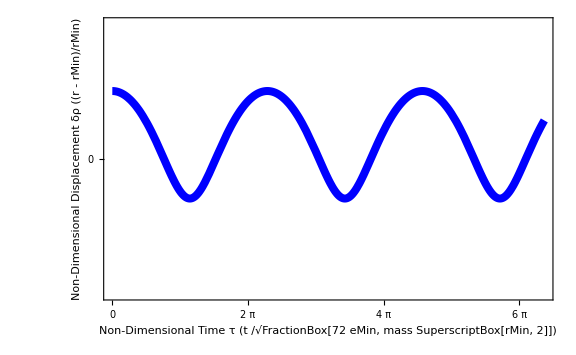

```mathematica
numericalSolutionPlot =Plot[aSolutionForParticularInitialConditions[t],{t,0,20},

]
```

Let’s compare this to the Harmonic Approximation

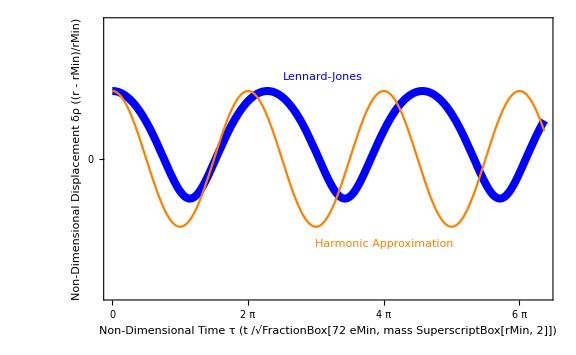

```mathematica
Show[numericalSolutionPlot,Plot[0.1 Cos[τ],{τ,0,20}, PlotStyle->Orange],

]
```

There are a few things to notice here that we will analyze a bit further later.

1) The period of the Lennard-Jones solution is greater than that of the Harmonic Oscillator (T=2π). This is because, on the average, the restoring force is a bit less for the Lennard-Jones potential.

2) The particle spends more time away from the particle it is interacting with (i.e., δρ>0) than nearer to it.  In other words, the average value of δρ is positive for the Lennard Jones potential and the average is zero for the Harmonic oscillator.

3) The particle’s speed is larger on the average when the displacement is negative (i.e., δρ<0). This is due to the large repulsive force.

We will characterize these observations, but first let’s generalize our solution to arbitrary initial conditions.

#### Generalizing the Numerical Solution

Our differential equation doesn’t depend on any parameters, but our initial conditions do. Because our differential equation is second-order, we have to specify two initial conditions: a position and a velocity (or momentum).

At first glance, it may seem like we have another two-dimensional parameter space to explore—but, it is only one dimensional.  Here’s why.  Any solution that goes through δρ=0 (i.e., at the potential’s minimum) will have a particular and unique—and maximum—value of kinetic energy (or velocity or momentum).  If we just start the clock at τ = 0 when δρ = 0, then we can explore our solutions as a function of the maximum kinetic energy.

Comment: Phase space and time reversal

The claim in the last paragraph is another way of saying that our solution completely covers phase space (i.e., the plane with position and momentum as axes; where the solutions are time-dependent curves; the map between the set of curves and phase space is bijective).

We will use this phase-space-way-of-looking-at-things later when we compute the partition function.

However, you might question whether each solution goes through δρ=0. After all, we could start the particle at δρ = δρ_o>0 and give it such a large positive momentum, p_o, that it never comes back.  This is where time reversal comes in.  We can get that same solution if we imagine that, at an earlier time, we start the particle at δρ=0 and give it such a larger negative momentum so that it has the same value, p_0, at δρ_o. Thus, we can always make the tractory go through zero by time reversal.

We can write a function that takes the maximum kinetic energy as an argument and calls NDSolve.

What is the best way to pass the kinetic energy argument to the function?  Non-dimensionalize of course. It is an energy quantity, so it makes sense to introduce:
κϵ  =  maxKE/E_min. 

Moreover, we will need to specify a non-dimensional velocity for the initial condition δρ’(0):




We used the minus-root because we will set the particle in motion so that separation decreases (details in comment above)

     (note the difference between the Greek “nu” and the Roman “v” here)

So, the expression for our initial condition is

```mathematica
νMax =Simplify[(- √((2 κϵ eMin)/mass))/(ωChar rMin), Assumptions->{eMin>0,rMin>0, mass>0}]
```

-(√κϵ)/6

```mathematica
ljSolution[dimensionlessMaxKE_]:=
(ljSolution[dimensionlessMaxKE] =
  NDSolveValue[
{newtonsEquationForLJ, δρ'[0] == (-Sqrt[dimensionlessMaxKE])/6, δρ[0]==0}, δρ,{τ,0,1000}])
```

Code Comment: Making functions and memoization

We’ve made a function for the first time above.  The details of coding and syntax will be dealt with later.  However, this is a brief how-to if you are curious.

Mathematica has many ways to create a function.  The following is the most common:
f[x_] := “do something with x”
or
g[x_,y_]:= “do something with x and y”

Here is an example. It is not very interesting, and will fail with the wrong kind of input. It’s just an example for now.

```mathematica
myFunction[shape_, color_]:=  Graphics[{color,shape[]},ImageSize->Tiny]
```

Examples of calling our function.

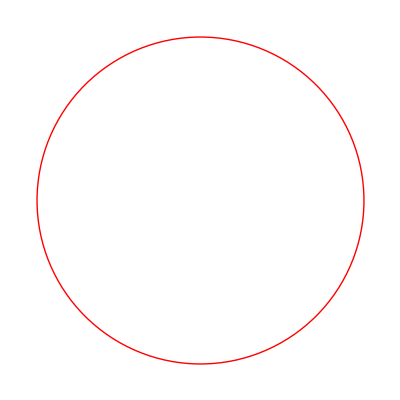

```mathematica
myFunction[Circle,Red]
```

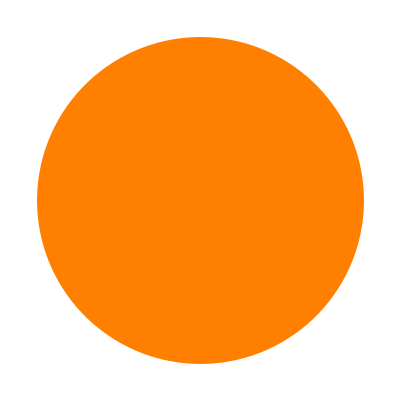

```mathematica
myFunction[Disk,Orange]
```

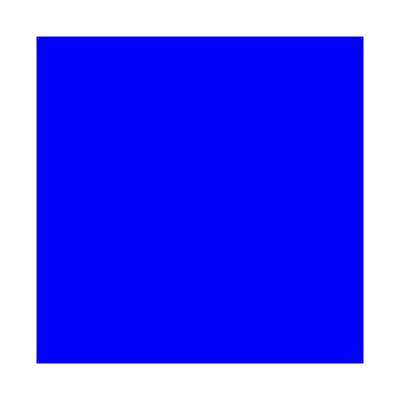

```mathematica
myFunction[Rectangle,Blue]
```

The function we created above (ljSolution) had something extra.  We constructed the function so it would “remember” a previous solution. So, the next time the function is called, it checks to see if it already has computed it. If so, it returns the previous result with no computation.  This is known as “memoization”.

Memoization definitions are like this:

f[x_] := f[x] = “do something with x”
It is the part   f[x] = “..” that is doing the memoization.
Here is an example

```mathematica
cpuIntensiveFunc[upperLimit_] := 
 cpuIntensiveFunc[upperLimit] =
  Total[
   Log[
    Table[
     NIntegrate[{x, y, z, t}^i, {x, 0, upperLimit},
      {y, 0, upperLimit},
      {z, 0, upperLimit},
      {t, 0, upperLimit}
      ]
     ,
     {i, FrobeniusSolve[{12, 16, 20, 27}, 500]}
     ]
    ]
   ]
```

The following call to the function will take around 10 seconds

```mathematica
cpuIntensiveFunc[Pi]
```

{4749.83,3788.42,3229.03,2310.59}

The next time it is computed for its value Pi, the function takes almost no time at all.

```mathematica
cpuIntensiveFunc[Pi]
```

{4749.83,3788.42,3229.03,2310.59}

Making a widget to plot our results:

```mathematica
DynamicModule[
{solutions = Table[ljSolution[k][t],{k,Range[.05,1.15,.05]}],
basePlot},
basePlot = Plot[solutions,{t,0,50},PlotStyle->{Opacity[0.33]},
];
Manipulate[Show[basePlot,Plot[ljSolution[k][t],{t,0,100}, PlotStyle->{Black,Thickness[0.005]}]],
{{k,},Range[.05,1.15,.05]}]
]
```

Notice that the period increases with the maximum kinetic energy until it reaches critical value;  above that energy the atom never returns to δρ = 0—it just keeps going and going.
Why is that?

#### Numerical Solutions with parameters

We had mentioned in a previous comment that numerical solvers cannot use symbolic parameters.  They can’t really, but the solver can return a function that is very efficient if it is given a number for a parameter later.  The next function gives all the functionality of a parametric solution to a differential equation.

Here is an example:

```mathematica
parametricNumSol =ParametricNDSolveValue[
{newtonsEquationForLJ, δρ'[0] == (-Sqrt[dimensionlessMaxKE])/6, δρ[0]==0}, δρ,{τ,0,1000},dimensionlessMaxKE]
```

ParametricFunction[<>]

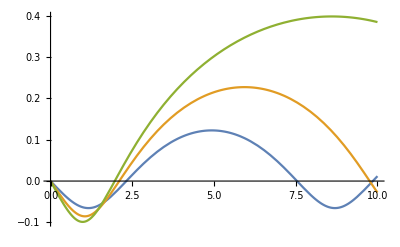

```mathematica
Plot[
{
parametricNumSol[.25][t],
parametricNumSol[.5][t],
parametricNumSol[.75][t]
}
,{t,0,10}]
```

### Computing the Period of Oscillation

The change of the period of oscillation with the maximum kinetic energy seems like an interesting result to explore.

We need a strategy to compute that.  Stop reading and take a few minutes to think about a strategy on your own.

Possible Strategies

We would like to compute the difference in time between cases where the separation and the velocity are the same.

Some strategies:
We could locate minima.  There are various routines to do that, such a FindMinimum, or we could write our own Newton-Raphson technique.

We know the initial position and velocity, we could follow the solution until it find the next position with the same velocity. A root-finding routine would do that, such as FindRoot.

There are more, but they all would requite more programming than we want to do right now.

So, we will use something called an EventLocator in our numerical solver.

Here is a solution that probably didn’t occur to you, it is a fairly advanced feature of NDSolve that looks for a particular event, and when it occurs it does something--in this case it stops the integration.  It is the
WhenEvent[δρ[τ]==0 &&  δρ’[τ]<0,{tPeriod = τ,”StopIntegration”}]
that does the trick for us, and it stores its result in tPeriod.

It’s just a simple addition to our previous function.

```mathematica
ljPeriod[dimensionlessMaxKE_]:=ljPeriod[dimensionlessMaxKE]=
Module[{tPeriod},
 NDSolveValue[
{newtonsEquationForLJ, δρ'[0] == (-Sqrt[dimensionlessMaxKE])/6, δρ[0]==0,WhenEvent[δρ[τ]==0 &&  δρ'[τ]<0,{tPeriod = τ,"StopIntegration"}]}, δρ,{τ,0,1000}];
tPeriod
]
```

This is an example of calling it

```mathematica
ljPeriod[0.5]
```

9.76194

We can plot the result.

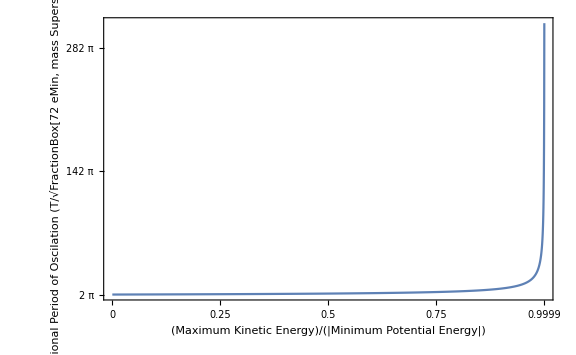

```mathematica
Plot[ljPeriod[ke],{ke,0,.9999},
]
```

The period of oscillation diverges, and this makes sense because if there is not enough potential energy to “reign in” the kinetic energy, the particle flies off to infinity. In other words, if  the initial condition is larger than the escape velocity.

### Creating a Pedagogical Interactive Visualization

```mathematica
With[{background = Plot[υLJP,{ρ,3/4,2},
 PlotLabel-> "Lennard-Jones Potential",
FrameLabel->{"r/r_min","Potential/E_min"},
BaseStyle->16,
Frame->True,ImageSize->Large
]},
Manipulate[
Animate[Show[background,Graphics[{Red,PointSize[0.05],With[{r=ljSolution[ke][t]},Point[{r+1,υLJP/.ρ->(r+1)}]]}]],
{{t,0,Style["Normalized Time",14]},0,Min[2 ljPeriod[ke],1000]},
DefaultDuration->Min[2 ljPeriod[ke],100]/2
],
{{ke,1/10,Style["Effective Temperature",14]},Range[1/10,1,1/10]}
]
]
```

### Computing Expected Values from Continuous Distributions

The expected value

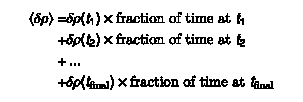
To find the expected (or average) value of a quantity like position, we would take the weighted average of positions at each increment of time:

-Graphics-



Taking time as a continuous variable and δρ as a continuous function:



In general, if p(x) is the probability density of finding x in slice (x, x + dx). (i.e., p(x) is a probability density, p(x) dx is the probability at x). 
Then the expected value of a quantity is:
  where

The expected value of displacement is:  

for example, when κϵ  = 0.2

When can make the expected displacement a function of the maximum kinetic energy:

```mathematica
expectedDisplacement[maxKinE_]:=NIntegrate[ljSolution[maxKinE][τ],{τ,0,ljPeriod[maxKinE]}]/ljPeriod[maxKinE]
```

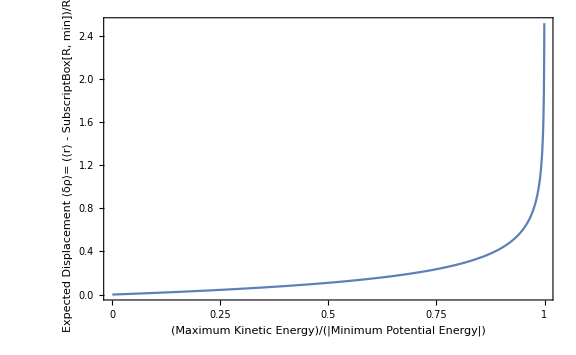

```mathematica
Plot[expectedDisplacement[ke],{ke,0,1},
]
```

The plot above indicates that the expected displacement between two interacting particles—when the bottom of the well is not symmetric as in the Lennard-Jones potential—is a function of the kinetic energy of the system.
This behaves like the thermal expansion coefficient which we will discuss in more detail below.  This is the explanation which is given in most textbooks.

Why does the expected displacement diverge with the initial kinetic energy is equal to (minus) the potential energy?

Temperature is related to the kinetic energy via the Boltzmann constant:
E_kin =(degrees of freedom)/2 k_B T 

The expected value of  kinetic energy is:

The factor of 72 comes from the non-dimensionalization

```mathematica
expectedκϵ[maxKinE_]:=With[{dρdτ =ljSolution[maxKinE]'}, (36NIntegrate[dρdτ[t]^2,{t,0,ljPeriod[maxKinE]}])/ljPeriod[maxKinE]
]
```

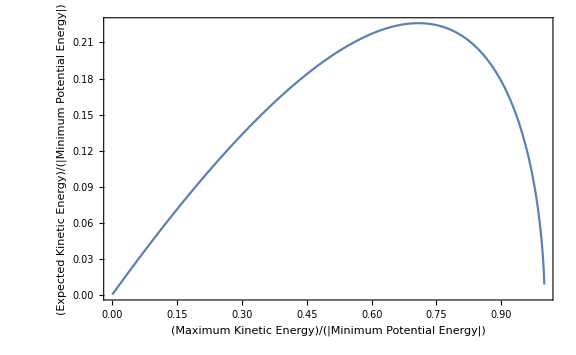

```mathematica
Plot[expectedκϵ[k], {k, 0, 1},
,Frame->True,BaseStyle->{FontSize->14},ImageSize->Large,PlotRange->All
]
```

So the average kinetic energy is not unique function of the maximum kinetic energy. This makes sense. At small oscillations, there isn’t much kinetic energy. With large initial kinetic energy, the particle spends almost all of its time at a large displacement and with a small velocity.  Thus, we are unable to make a one-to-one correspondence to maximum kinetic energy and temperature.
The explanation  about average displacement relating to temperature isn’t correct.

It is always a good idea to do a sanity check.  Let’s check and see if the kinetic energy plus the potential energy is constant

```mathematica
Manipulate[
With[{ρ=1+ljSolution[ke][τ], ρdot =ljSolution[ke]'[τ]},
Plot[
{72 ρdot^2/2,1/ρ^12-2/ρ^6, 72 ρdot^2/2+(1/ρ^12-2/ρ^6)
},{τ,0,ljPeriod[ke]},

]],
{ke,.001,.99}
]
```